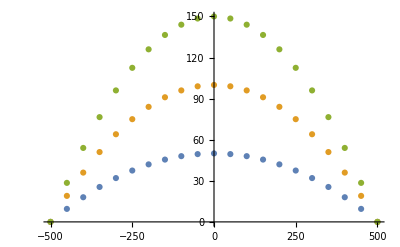

```mathematica
(*--- path ---*)
dirCT="C:\\Users\\PC_Gr\\OneDrive - Università degli Studi di Catania\\2023-05-04_SURSO\\excalidraw";
dirME="C:\\Users\\39393\\OneDrive - Università degli Studi di Catania\\2023-05-04_SURSO\\excalidraw";
dirNB="C:\\xampp\\htdocs\\exblog\\content\\assets";
dir=dirNB;
SetDirectory[dir];

(*--- packages ---*)
Needs["utilities`"];
Needs["excalidraw`"];

(*--- main ---*)

xI=-500;
xJ=500;
dx=50;

excalidraw=<|
"type"->"excalidraw",
"version"->2,
"source"->"https://excalidraw.com",
"elements"->{},
"appState"-><|
"gridSize"->dx,
"viewBackgroundColor"->"#ffffff"
|>,
"files"-><||>
|>;

(* elements *)
Lines={<|"yMax"->50,"color"->"#1864ab"|>,<|"yMax"->100,"color"->"#087f5b"|>,<|"yMax"->150,"color"->"#c92a2a"|>};

elements={};
points={};
Do[{

yMax=Lines[[l]][["yMax"]];
color=Lines[[l]][["color"]];

a=yMax/(xI xJ);b=-(yMax (xI+xJ))/(xI xJ);
points01=Table[{x,a x^2+b x+yMax},{x,xI,xJ,dx}];
Line01=<|"width"->xJ-xI,"height"->yMax,"points"->points01,"strokeColor"->color,"strokeWidth"->4|>;

AppendTo[points,points01];
AppendTo[elements,exdwLine[Line01]];
},{l,1,Lines//Length}];

lp=ListPlot[points];
If[0==1,Print[lp]];

excalidraw["elements"]=elements;
Export["logo.excalidraw",excalidraw,"RawJSON"];

uDebug[];
```